```mathematica
T=Import["/Users/sophi529/Documents/Non college/2016 Summer/Indiana/Lab stuff/CTRNN/MultiLeggedWalker2/twolegtest/1.dat"];
```

```mathematica
BestVsGen[L_]:=Map[{#⟦1⟧,#⟦2⟧}&,L]
```

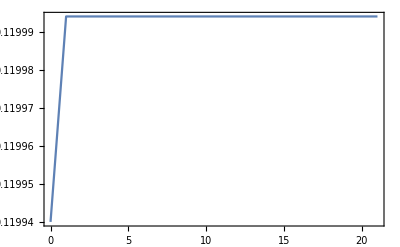

```mathematica
ListLinePlot[BestVsGen[T],Frame->True]
```